```mathematica
SetDirectory["/Users/mbibireata/Documents/GitHub/Networks/figures"]
```

/Users/mbibireata/Documents/GitHub/Networks/figures

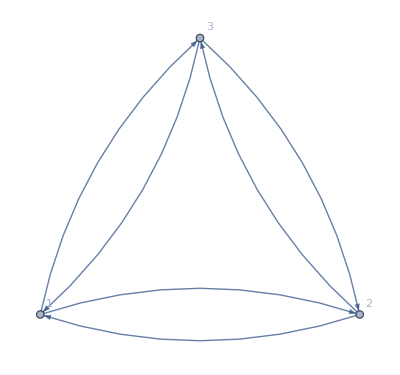

```mathematica
g1=Graph[{1->2,2->3,3->1,2->1,3->2,1->3},(*PlotLabel->"Directed 2-Core of Size 3",*)VertexLabels->Automatic]
```

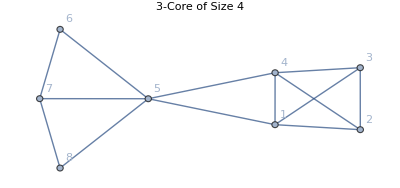

```mathematica
(* Graph with 4 vertices *) 
g2=Graph[{1<->2, 2<->3, 3<->4,1<->4, 1<->3, 2<->4, 4<->5, 1<->5, 5<->6, 6<->7, 7<->8, 8<->5, 7<->5},PlotLabel->"3-Core of Size 4",VertexLabels->Automatic]
```

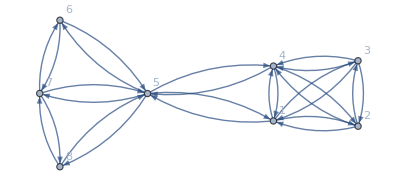

```mathematica
(* Same Graph but Directed *)
g2Prime = Graph[{1->2, 2->3, 3->4, 4->1, 2->1, 3->2, 3->4, 1->4,3->1, 1->3, 4->2, 2->4, 4->5, 5->4, 1->5, 5->1, 5->6, 6->5, 6->7, 7->6, 7->5,5->7, 7->8, 8->7, 8->5, 5->8}, VertexLabels->Automatic]
```

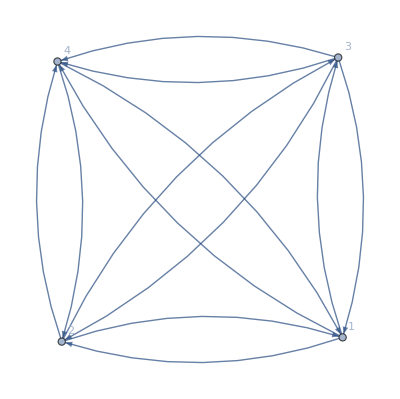

```mathematica
g3=Graph[{1->2, 2->3, 3->4, 4->1, 2->1, 3->2, 3->4, 1->4,3->1, 1->3, 4->2, 2->4},VertexLabels->Automatic]
```

```mathematica
Export["g1.png",g1]
Export["g2.png",g2Prime]
Export["g3.png",g3]
```

g1.png

g2.png

g3.png

(0 | 1 | 1 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)

mat_test.png

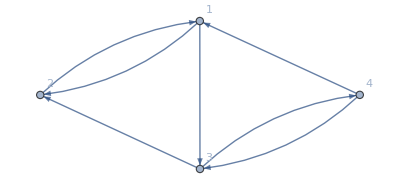

adj_mat_sample.png

```mathematica
(* Adjacency matrix to graph *) 
mat={{0,1,1,0},{1,0,0,0},{0,1,0,1},{1,0,1,0}};
mat//MatrixForm
Export["mat_test.png",mat//MatrixForm]
g4=AdjacencyGraph[mat,VertexLabels->Automatic]
Export["adj_mat_sample.png",g4]
```